# Hands-on Start to Mathematica

## Basic input

```mathematica
627 / 3
```

209

```mathematica
628 / 3
```

628/3

```mathematica
N[628/3]
```

209.333

## Free-form input

WolframAlphaQueryParseResults

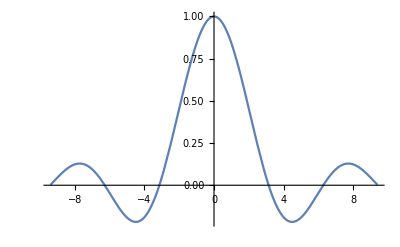

WolframAlphaQueryParseResults

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

WolframAlphaQueryParseResults

{{x→7/2,y→21/4}}

WolframAlphaQueryParseResults

ArcTan[(-1+2 x)/(√3)]/(√3)+1/3 Log[1+x]-1/6 Log[1-x+x^2]

```mathematica
MoleculePlot3D[Entity["Chemical","Caffeine"]]
```

## Wolfram Language input

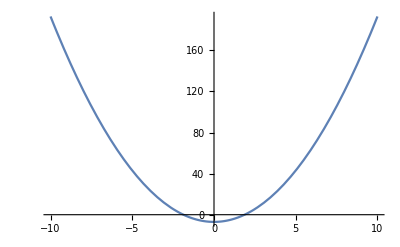

```mathematica
Plot[2x ^ 2- 7, {x, -10, 10}]
```

```mathematica
Plot3D[Sin[x * y], {x, -3, 3}, {y, -3, 3}]
```

-Graphics3D-

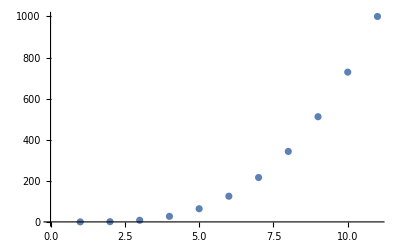

```mathematica
Table[i ^ 3, {i, 0 , 10}];
ListPlot[%]
```

```mathematica
mat1 = {{1, 3, -2}, {2, 5, 0}, {-3, -5, 7}};
Det[mat1]
```

-17

```mathematica
Clear[mat1]
```

## Applying what we’ve learned

```mathematica
Manipulate[Plot[Sin[freq * x], {x, 0, 6*Pi}, PlotRange -> {-4, 4}], {freq, 1, 5}]
```

```mathematica
Manipulate[Plot[amp * func[freq * x], {x, 0, 6*Pi}, PlotRange -> {-4, 4}], {amp, 1, 4}, {freq, 1, 5}, {func, {Sin, Cos, Tan}}]
```

## Documentation & saving

-Graphics3D-